### General 2HDM

```mathematica
path=NotebookDirectory[]
```

/home/leonardoferreira/hhh/

```mathematica
Get[StringJoin[path,"massesTOlambda.m"]];
```

```mathematica
lis={};
λmax=4*Pi;
lisper={};
lissta={};
lisT={};
Print["Setting charged and CP-even masses equal"]
Do[
vv=246;
tanb=RandomReal[{1.5,100/20}];
be=ArcTan[tanb];
sb=Sin[be];
cb=Cos[be];
l5=RandomReal[{-λmax,λmax}];
l6=0;
l7=0;
mh=RandomReal[{125,125}];
ma=RandomReal[{mh,1000}];
m122=m122N[ma,sb,cb,vv,l5,l6,l7];
mH=RandomReal[{mh,1000}];
mHp=RandomReal[{mh,1000}];
mHp=mH;
al=be-Pi/2;
l1=λ1[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];l2=λ2[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];
l3=λ3[mH,mh,mHp,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];
l4=λ4[ma,mHp,m122,Sin[be],Cos[be],vv,l6,l7];
M=m122/(Sin[be]*Cos[be]);
vhhh=-(3*mh^2)/(2*vv*Sin[2*be])*(Cos[3*al-be]+3*Cos[al+be]-4*Cos[al-be]^2*Cos[al+be]*M/mh^2)-3*mh^2/vv*(mH^4/(12 Pi^2 mh^2 vv^2)*(1-M/mH^2)^3+ma^4/(12 Pi^2 mh^2 vv^2)*(1-M/ma^2)^3+mHp^4/(6 Pi^2 mh^2 vv^2)*(1-M/mHp^2)^3+(-(3*(176)^4)/(3*Pi^2*mh^2*vv^2)));
(*save all points*)(*AppendTo[lis,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,Abs@vhhh}];*)
(*save points that comply with perturbativity - λmax *)If[-λmax<l1<λmax&&-λmax<l2<λmax&&-λmax<l3<λmax&&-λmax<l4<λmax&&-λmax<l5<λmax,AppendTo[lisper,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,-vhhh}]];
(*save points that comply with stability of potential *)
If[0<l1&&0<l2&&-(l1*l2)^(1/2)<l3&&l3+l4-Abs[l5]>-(l1*l2)^(1/2),AppendTo[lissta,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,-vhhh}]];
(*save points that comply with perturbativity AND stability *)
If[0<l1<λmax&&0<l2<λmax&&-λmax<l3<λmax&&-(l1*l2)^(1/2)<l3&&-λmax<l4<λmax&&-λmax<l5<λmax&&l3+l4-Abs[l5]>-(l1*l2)^(1/2),AppendTo[lisT,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,M,-vhhh}]],
{i,10000}]
```

Setting charged and CP-even masses equal

```mathematica
name={"mh","mH","ma","mHp","Cos α","Tan β","λ1","λ2","λ3","λ4","λ5","λ6","λ7","M","vhhh"};
```

```mathematica
numsta=lissta;
Print["STABILITY"]
Dimensions@numsta
numper=lisper;
Print["PERTURBATIVITY"]
Dimensions@numper
numT=lisT;
Print["ALL"]
Dimensions@numT
```

STABILITY

{3996,14}

PERTURBATIVITY

{1155,14}

ALL

{367,15}

```mathematica
(* Plot considering only points that pass all constraints *)
```

```mathematica
plotN[a1_,a2_]:=ListPlot[{Transpose@{numT[[All,a1]],numT[[All,a2]]}},Frame->True,PlotRange->Full,FrameLabel->{name[[a1]],name[[a2]]},PlotStyle->{Directive[Black,PointSize[0.012]]}]
```

```mathematica
(* Some examples *)
```

```mathematica
Table[{i,name[[i]]},{i,Length@name}]
```

{{1,mh},{2,mH},{3,ma},{4,mHp},{5,Cos α},{6,Tan β},{7,λ1},{8,λ2},{9,λ3},{10,λ4},{11,λ5},{12,λ6},{13,λ7},{14,M},{15,vhhh}}

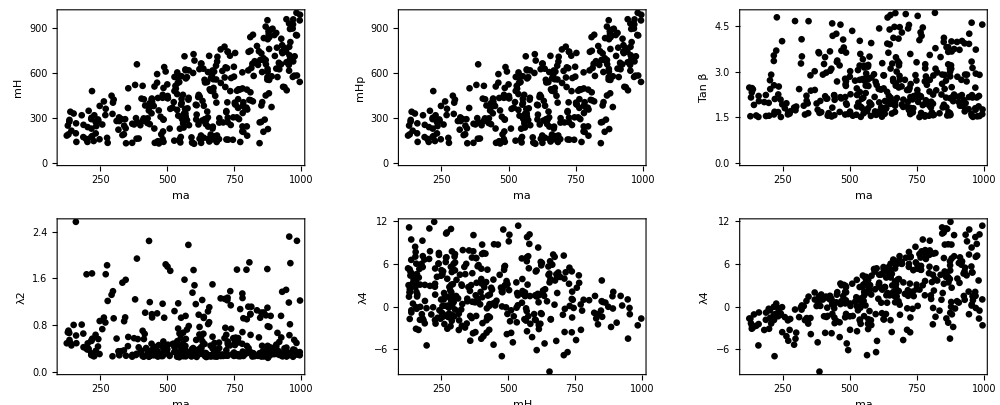

```mathematica
GraphicsGrid[{{plotN[3,2],plotN[3,4],plotN[3,6]},{plotN[3,8],plotN[2,10],plotN[3,10]}},ImageSize->1000]
```

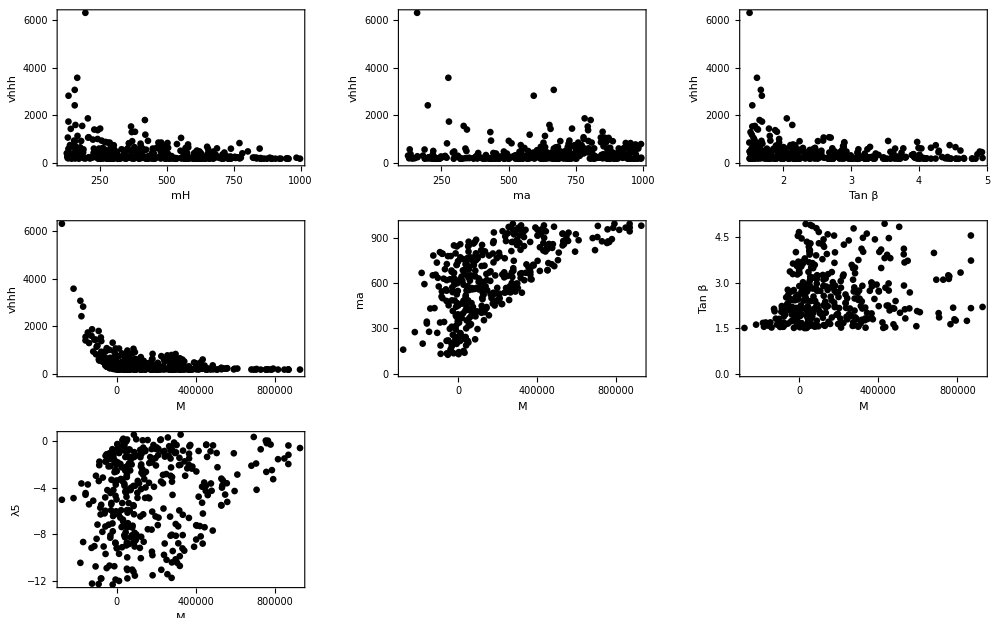

```mathematica
GraphicsGrid[{{plotN[2,-1],plotN[3,-1],plotN[6,-1]},{plotN[14,-1],plotN[14,3],plotN[14,6]},{plotN[14,11]}},ImageSize->1000]
```

```mathematica
(* Plot to compare points regarding distinct constraints *)
```

```mathematica
Clear[plot]
plot[a1_,a2_]:=ListPlot[{Transpose@{numsta[[All,a1]],numsta[[All,a2]]},Transpose@{numper[[All,a1]],numper[[All,a2]]},Transpose@{numT[[All,a1]],numT[[All,a2]]}},Frame->True,PlotRange->Full,FrameLabel->{name[[a1]],name[[a2]]},PlotStyle->{Directive[Blue,PointSize[0.01]],Directive[Red,PointSize[0.01]],Directive[Black,PointSize[0.012]]}];
```

```mathematica
(* Some examples *)
```

```mathematica
Table[{i,name[[i]]},{i,Length@name}]
```

{{1,mh},{2,mH},{3,ma},{4,mHp},{5,Cos α},{6,Tan β},{7,λ1},{8,λ2},{9,λ3},{10,λ4},{11,λ5},{12,λ6},{13,λ7},{14,M},{15,vhhh}}

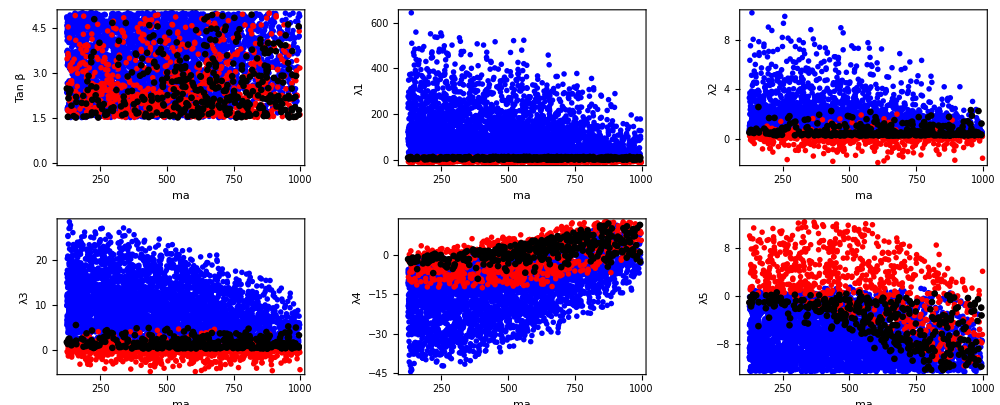

```mathematica
GraphicsGrid[{{plot[3,6],plot[3,7],plot[3,8]},{plot[3,9],plot[3,10],plot[3,11]}},ImageSize->1000]
```

### 2HDM - setting λ_5=0

```mathematica
path=NotebookDirectory[]
```

/home/leonardoferreira/hhh/

```mathematica
Get[StringJoin[path,"massesTOlambda.m"]];
```

```mathematica
lis={};
λmax=4*Pi;
lisper={};
lissta={};
lisT={};
Do[
vv=246;
tanb=RandomReal[{1.5,100/20}];
be=ArcTan[tanb];
sb=Sin[be];
cb=Cos[be];
l5=RandomReal[{-10^-1,10^-1}]*0;
l6=0;
l7=0;
mh=RandomReal[{125,125}];
ma=RandomReal[{mh,1000}];
m122=m122N[ma,sb,cb,vv,l5,l6,l7];
mH=RandomReal[{mh,1000}];
mHp=RandomReal[{mh,1000}];
al=be-Pi/2;
l1=λ1[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];l2=λ2[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];
l3=λ3[mH,mh,mHp,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7];
l4=λ4[ma,mHp,m122,Sin[be],Cos[be],vv,l6,l7];
M=m122/(Sin[be]*Cos[be]);
vhhh=-(3*mh^2)/(2*vv*Sin[2*be])*(Cos[3*al-be]+3*Cos[al+be]-4*Cos[al-be]^2*Cos[al+be]*M/mh^2)-3*mh^2/vv*(mH^4/(12 Pi^2 mh^2 vv^2)*(1-M/mH^2)^3+ma^4/(12 Pi^2 mh^2 vv^2)*(1-M/ma^2)^3+mHp^4/(6 Pi^2 mh^2 vv^2)*(1-M/mHp^2)^3+(-(3*(176)^4)/(3*Pi^2*mh^2*vv^2)));
(*save all points*)(*AppendTo[lis,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,Abs@vhhh}];*)
(*save points that comply with perturbativity - λmax *)If[-λmax<l1<λmax&&-λmax<l2<λmax&&-λmax<l3<λmax&&-λmax<l4<λmax&&-λmax<l5<λmax,AppendTo[lisper,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,M,-vhhh}]];
(*save points that comply with stability of potential *)
If[0<l1&&0<l2&&-(l1*l2)^(1/2)<l3&&l3+l4-Abs[l5]>-(l1*l2)^(1/2),AppendTo[lissta,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,M,-vhhh}]];
(*save points that comply with perturbativity AND stability *)
If[0<l1<λmax&&0<l2<λmax&&-λmax<l3<λmax&&-(l1*l2)^(1/2)<l3&&-λmax<l4<λmax&&-λmax<l5<λmax&&l3+l4-Abs[l5]>-(l1*l2)^(1/2),AppendTo[lisT,{mh,mH,ma,mHp,Cos[al],Tan[be],l1,l2,l3,l4,l5,l6,l7,M,-vhhh}]],
{i,10000}]
```

```mathematica
name={"mh","mH","ma","mHp","Cos α","Tan β","λ1","λ2","λ3","λ4","λ5","λ6","λ7","M","vhhh"};
```

```mathematica
numsta=lissta;
Print["STABILITY"]
Dimensions@numsta
numper=lisper;
Print["PERTURBATIVITY"]
Dimensions@numper
numT=lisT;
Print["ALL"]
Dimensions@numT
```

STABILITY

{3726,15}

PERTURBATIVITY

{1391,15}

ALL

{443,15}

```mathematica
(* Plot considering only points that pass all constraints *)
```

```mathematica
plotN[a1_,a2_]:=ListPlot[{Transpose@{numT[[All,a1]],numT[[All,a2]]}},Frame->True,(*PlotRange->{{125,900},{125,900}},*)PlotRange->Full,AspectRatio->1,FrameLabel->{name[[a1]],name[[a2]]},PlotStyle->{Directive[Black,PointSize[0.012]]}]
```

```mathematica
(* Some examples *)
```

```mathematica
Table[{i,name[[i]]},{i,Length@name}]
```

{{1,mh},{2,mH},{3,ma},{4,mHp},{5,Cos α},{6,Tan β},{7,λ1},{8,λ2},{9,λ3},{10,λ4},{11,λ5},{12,λ6},{13,λ7},{14,M},{15,vhhh}}

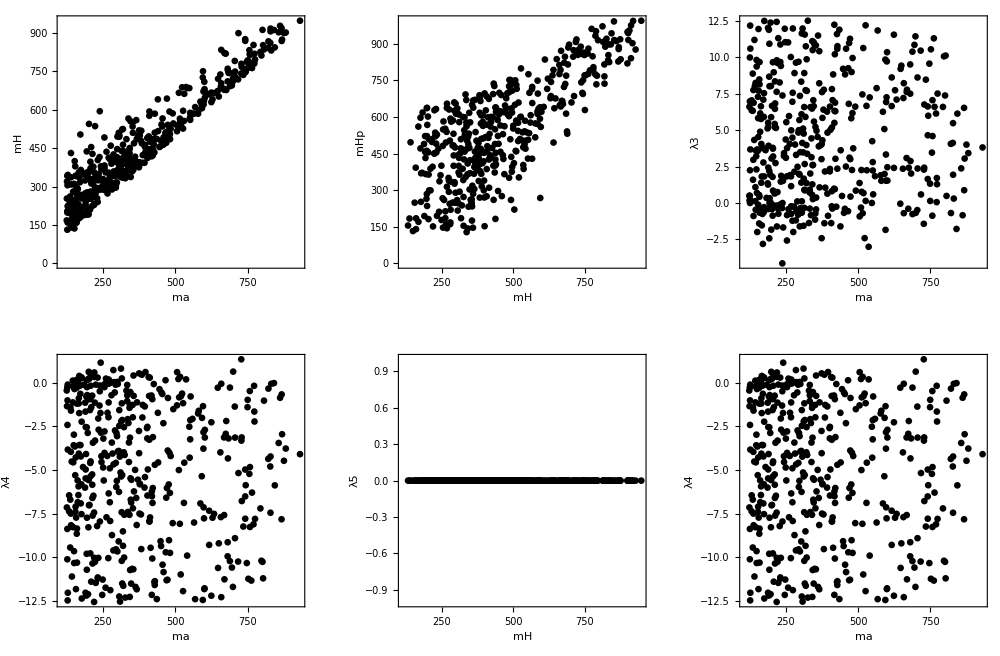

```mathematica
GraphicsGrid[{{plotN[3,2],plotN[2,4],plotN[3,9]},{plotN[3,10],plotN[2,11],plotN[3,10]}},ImageSize->1000]
```

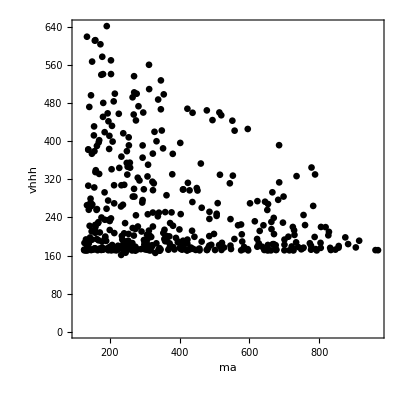

```mathematica
plotN[3,15]
```

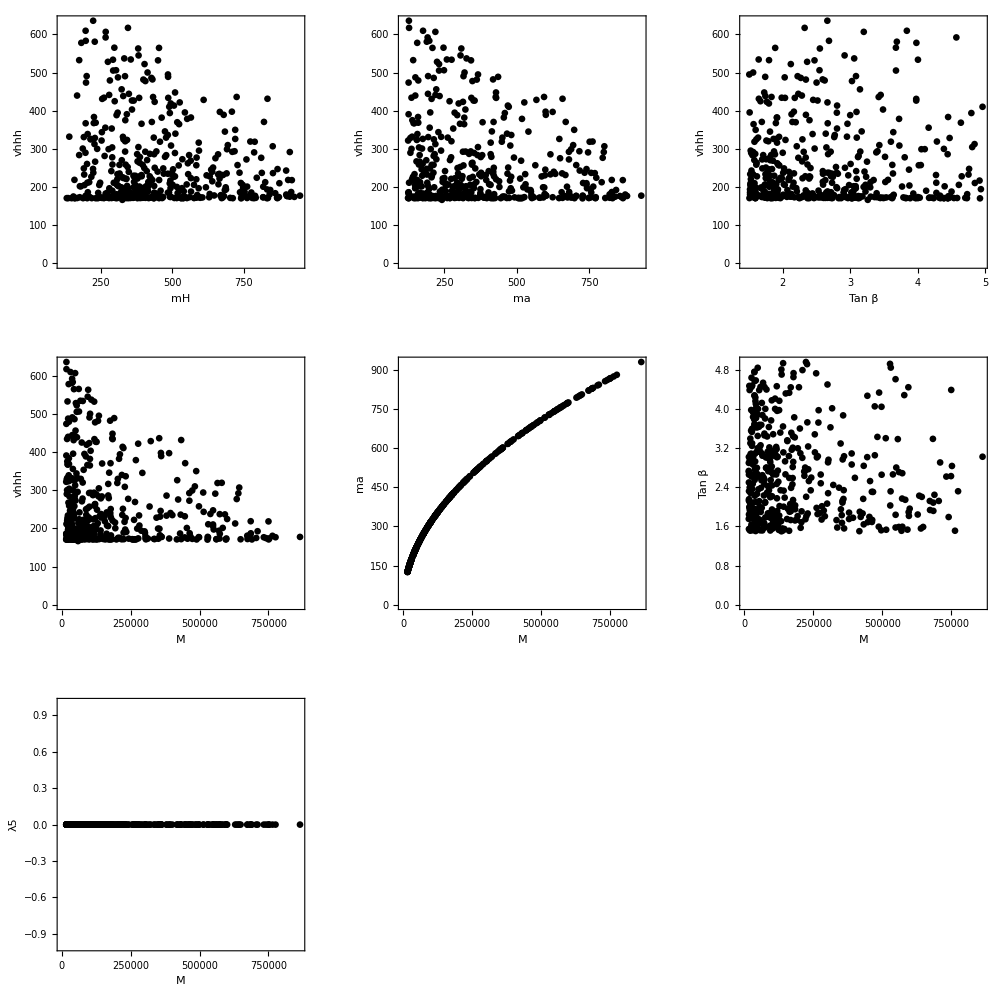

```mathematica
GraphicsGrid[{{plotN[2,-1],plotN[3,-1],plotN[6,-1]},{plotN[14,-1],plotN[14,3],plotN[14,6]},{plotN[14,11]}},ImageSize->1000]
```

```mathematica
(* Plot to compare points regarding distinct constraints *)
```

```mathematica
Clear[plot]
plot[a1_,a2_]:=ListPlot[{Transpose@{numsta[[All,a1]],numsta[[All,a2]]},Transpose@{numper[[All,a1]],numper[[All,a2]]},Transpose@{numT[[All,a1]],numT[[All,a2]]}},Frame->True,PlotRange->Full,FrameLabel->{name[[a1]],name[[a2]]},PlotStyle->{Directive[Blue,PointSize[0.01]],Directive[Red,PointSize[0.01]],Directive[Black,PointSize[0.012]]}];
```

```mathematica
(* Some examples *)
```

```mathematica
Table[{i,name[[i]]},{i,Length@name}]
```

{{1,mh},{2,mH},{3,ma},{4,mHp},{5,Cos α},{6,Tan β},{7,λ1},{8,λ2},{9,λ3},{10,λ4},{11,λ5},{12,λ6},{13,λ7},{14,M},{15,vhhh}}

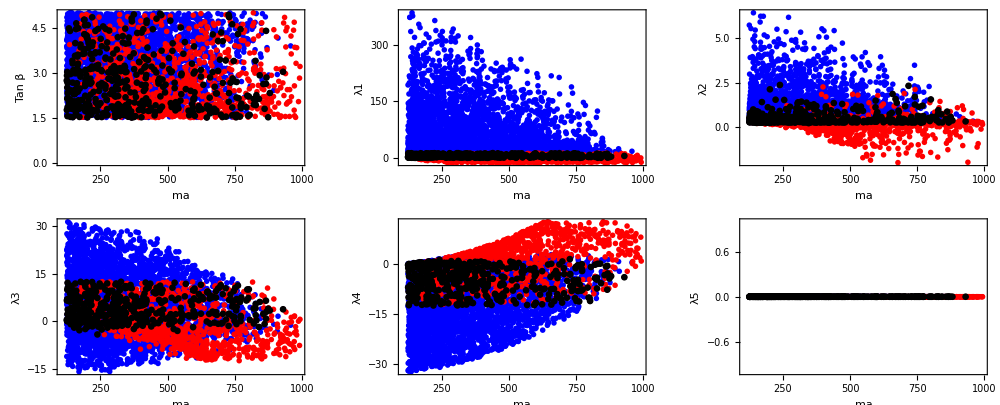

```mathematica
GraphicsGrid[{{plot[3,6],plot[3,7],plot[3,8]},{plot[3,9],plot[3,10],plot[3,11]}},ImageSize->1000]
```

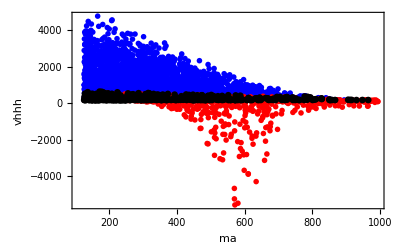

```mathematica
plot[3,15]
```

```mathematica
Export[StringJoin[path,"Kanemura_data.csv"],numT]
```

/home/leonardoferreira/hhh/Kanemura_data.csv

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["/home/leonardoferreira/hhh/Kanemura_data.csv"]]]
```

```mathematica
{ma,mH,mHp,al,be,l5}={843.7130109072517, 932.5367453180893, 943.752106876145,ArcCos@-0.8670633580416512 ,ArcTan@1.7403995143978208,0}
```

{843.713,932.537,943.752,2.62007,1.04928,0}

```mathematica
vv=251
```

251

```mathematica
(m122N[ma,Sin[be],Cos[be],vv,l5,l6,l7]/(Sin[be]Cos[be]))//Sqrt
m122=m122N[ma,Sin[be],Cos[be],vv,l5,l6,l7]
```

843.713

307498.

```mathematica
l1=λ1[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7]
l2=λ2[mH,mh,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7]
l3=λ3[mH,mh,mHp,m122,Cos[al],Sin[al],Sin[be],Cos[be],vv,l6,l7]
l4=λ4[ma,mHp,m122,Sin[be],Cos[be],vv,l6,l7]
```

7.8335

1.07479

3.42034

-5.67662

```mathematica
M=(m122N[ma,Sin[be],Cos[be],vv,l5,l6,l7]/(Sin[be]Cos[be]))
```

711852.

```mathematica
-(3*mh^2)/(2*vv*Sin[2*be])*(Cos[3*al-be]+3*Cos[al+be]-4*Cos[al-be]^2*Cos[al+be]*M/mh^2)-3*mh^2/vv*(mH^4/(12 Pi^2 mh^2 vv^2)*(1-M/mH^2)^3+ma^4/(12 Pi^2 mh^2 vv^2)*(1-M/ma^2)^3+mHp^4/(6 Pi^2 mh^2 vv^2)*(1-M/mHp^2)^3+(-(3*(176)^4)/(3*Pi^2*mh^2*vv^2)))
```

177.396

```mathematica
-(3*mh^2)/(2*vv*Sin[2*be])*(Cos[3*al-be]+3*Cos[al+be]-4*Cos[al-be]^2*Cos[al+be]*M/mh^2)
```

186.753

```mathematica
177.3964274813249/186.7529880478088
```

0.949899